```mathematica
ToJson[keys_,values_]:=ExportString[MapThread[Function[{x,y}, ToString[x]->Replace[y, ComplexInfinity->Null, 3]], {keys,values}], "JSON"]
Equation16[x_, y_, yp_]:=Module[{mu2},
mu2 = Equation15[x, y, yp];
x yp (mu2 - 1)/(CalcA[x, y, yp]mu2 + CalcB[x, y, yp])
]
Equation15[x_, y_, yp_]:=If[x==1&&(y^2-yp^2==0||y^2-yp^2==1), 0, 1-2x (1-x)/(2 (1-x) - (y^2 - yp^2) + Sqrt[(y^2 - yp^2)^2 + 4(1-x)^2yp^2])]
Equation14[x_, y_, yp_, yt_]:=If[y==0, 1,yt/(yp - 1/2 (y^2 - yp^2)Equation16[x, y, yp])]
Equation13[x_, y_, yp_, yt_]:=Module[{pt},
pt = Equation14[x, y, yp, yt];
If[y==0, Null,pt(pt - 1/2(yt - yp pt)Equation16[x, y, yp]) - 1]
]
Equation14Normal[x_,y_,yp_,pt_]:=pt * (CalcA[x, y, yp]*Equation15[x, y, yp] + CalcB[x, y, yp])
CalcA[x_, y_, yp_]:= 1 -  x - y^2 + x yp^2
CalcB[x_, y_, yp_]:=-(1-x)(1-x-y^2) + 1/2 x y^2 - 1/2 x yp^2
CalcC[x_, y_, yp_]:=(1 - x)((1 - x)^2 - y^2)
CalcYP[x_,y_,yt_]:=If[y==0, 0, yp//.N[ResourceFunction["BisectionMethodFindRoot"][Equation13[x,y,yp,yt], {yp, -y-0.000000002,y+0.00000001}, 1*^-8, 500], 10]]
AppendYP[x_,y_,yt_]:={x, y, CalcYP[x,y,yt], yt}
```

```mathematica
(*{x, y, yt}*)
CheckInputs = {
{0.12299999990950466,0.000999999920722544,0.00009999994540457024},
{1.633999999924627,3.233999999900874,0.419999999924224},
{1.2629999999554258,1.099999999963894,-7.622408860462292*^-12},
{1.642999999990003,1.0099999999783544,-0.23400000001807722},
{10.429999999908397,4.234999999951009,-10.234000000034976},
{46.64157468120425,31.848918494200568,-5.055719635576005}
};
RandomCap = 50;
ZeroInputs =Table[{RandomReal[{-RandomCap, RandomCap}], 0, 0},10];
RandomInputs =
Table[ Module[{y},
y=RandomReal[{0, RandomCap}];
{RandomReal[{0, RandomCap}], y, y*RandomReal[]}
], 10];
AllInputs = ToJson[ Join[CheckInputs, RandomInputs]];
AOutputsInputs = ToJson[{"SetInputs", "RandomInputs",  "ZeroInputs"},{Transpose[{CheckInputs, CalcA @@@CheckInputs}],Transpose[{RandomInputs, CalcA @@@RandomInputs}], Transpose[{ZeroInputs, CalcA @@@ZeroInputs}]}];
BOutputsInputs = ToJson[{"SetInputs", "RandomInputs",  "ZeroInputs"},{Transpose[{CheckInputs, CalcB @@@CheckInputs}],Transpose[{RandomInputs, CalcB @@@RandomInputs}], Transpose[{ZeroInputs, CalcB @@@ZeroInputs}]}];
COutputsInputs = ToJson[{"SetInputs", "RandomInputs",  "ZeroInputs"},{Transpose[{CheckInputs, CalcC @@@CheckInputs}],Transpose[{RandomInputs, CalcC @@@RandomInputs}], Transpose[{ZeroInputs, CalcC @@@ZeroInputs}]}];
DLNYDYP =  ToJson[{"SetInputs", "RandomInputs",  "ZeroInputs"},{Transpose[{CheckInputs, Equation16 @@@CheckInputs}],Transpose[{RandomInputs, Equation16 @@@RandomInputs}], Transpose[{ZeroInputs, Table[Null, Length[ZeroInputs]]}]}];
MuSquared = ToJson[{"SetInputs", "RandomInputs",  "ZeroInputs"},{Transpose[{CheckInputs, Equation15 @@@CheckInputs}],Transpose[{RandomInputs, Equation15 @@@RandomInputs}], Transpose[{ZeroInputs, Equation15 @@@ZeroInputs}]}];
YPOutput = ToJson[{"SetInputs", "RandomInputs", "ZeroInputs"},{Transpose[{CheckInputs, CalcYP @@@CheckInputs}],Transpose[{RandomInputs, CalcYP @@@RandomInputs}], Transpose[{ZeroInputs, CalcYP @@@ZeroInputs}]}];
Equation14Output=ToJson[{"SetInputs", "RandomInputs", "ZeroInputs"},{Transpose[{AppendYP @@@CheckInputs, Equation14@@@AppendYP @@@CheckInputs}],Transpose[{AppendYP @@@RandomInputs, Equation14 @@@AppendYP @@@RandomInputs}], Transpose[{AppendYP @@@ZeroInputs, Equation14 @@@AppendYP @@@ZeroInputs}]}];
Equation13Output=ToJson[{"SetInputs", "RandomInputs", "ZeroInputs"},{Transpose[{AppendYP @@@CheckInputs, Equation13@@@AppendYP @@@CheckInputs}],Transpose[{AppendYP @@@RandomInputs, Equation13 @@@AppendYP @@@RandomInputs}], Transpose[{AppendYP @@@ZeroInputs, Equation13 @@@AppendYP @@@ZeroInputs}]}];
```

```mathematica
Equation13[tests[[1]], tests[[2]],tests[[2]], tests[[3]]]
Equation13[tests[[1]], tests[[2]],100, tests[[3]]]
```

-0.000112107

-0.140111

1.17817×10^-8

-1.

-1.62398×10^-7

-2.15673×10^-7

2.63712×10^-14

-1.

0.0010001

```mathematica
Function[{x,y,yt},Equation13[x,y,y+0.00000001,yt]]@@@CheckInputs
Function[{x,y,yt},Equation14[x,y,y+0.00000001,yt]]@@@CheckInputs
Function[{x,y,yt},Equation16[x,y,y+0.00000001]]@@@CheckInputs
Function[{x,y,yt},Equation13[x,y,-y-0.00000001,yt]]@@@CheckInputs
Function[{x,y,yt},Equation14[x,y,-y-0.00000001,yt]]@@@CheckInputs
Function[{x,y,yt},Equation16[x,y,-y-0.00000001]]@@@CheckInputs
Function[{x,y,yt},Equation13[x,y,0.00000001,yt]]@@@CheckInputs
Function[{x,y,yt},Equation14[x,y,0.00000001,yt]]@@@CheckInputs
Function[{x,y,yt},Equation16[x,y,0.00000001]]@@@CheckInputs
```

{-0.99,-0.983134,-1.,-0.946341,4.83961,-0.974801}

{0.099999,0.12987,-6.92946×10^-12,-0.231683,-2.41653,-0.158741}

{-0.140111,1.15366,48.0228,255.52,0.341899,0.0331263}

{-0.99,-0.983134,-1.,-0.946341,4.83961,-0.974801}

{-0.099999,-0.12987,6.92946×10^-12,0.231683,2.41653,0.158741}

{0.140111,-1.15366,-48.0228,-255.52,-0.341899,-0.0331263}

{7.92966×10^7,2.54254×10^14,-1.,7.83858×10^13,8.01675×10^15,1.12614×10^14}

{8904.86,1.59453×10^7,-0.000336828,-8.85358×10^6,-8.95363×10^7,-1.0612×10^7}

{-0.00245962,-3.12465×10^-9,-2.0876×10^-8,-3.22125×10^-8,-1.16307×10^-8,-9.19631×10^-10}

```mathematica
CheckInputs
```

{{0.123,0.001,0.0000999999},{1.634,3.234,0.42},{1.263,1.1,-7.62241×10^-12},{1.643,1.01,-0.234},{10.43,4.235,-10.234},{46.6416,31.8489,-5.05572}}

```mathematica
Equation13[x_, y_, yp_, yt_]:=Module[{pt},
pt = Equation14[x, y, yp, yt];
If[y==0, Null,pt(pt - 1/2(yt - yp pt)Equation16[x, y, yp]) - 1]
]
```

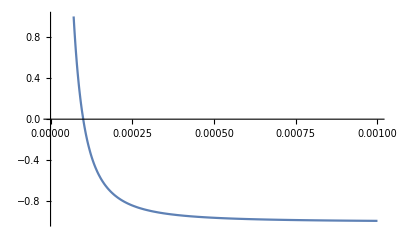
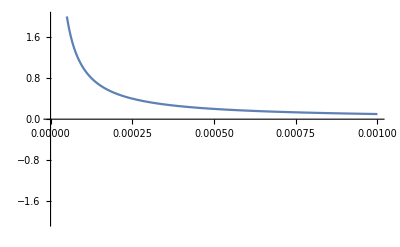
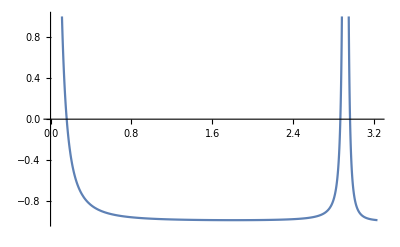
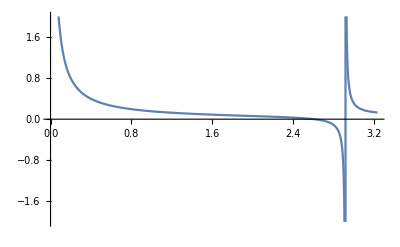
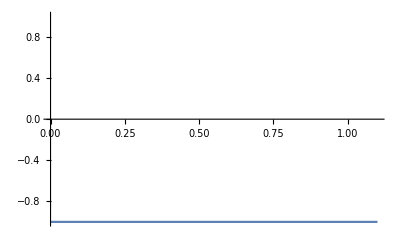
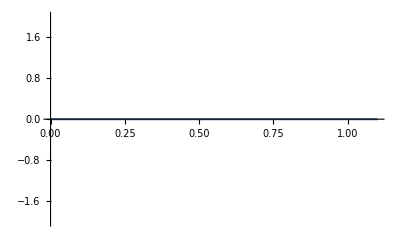
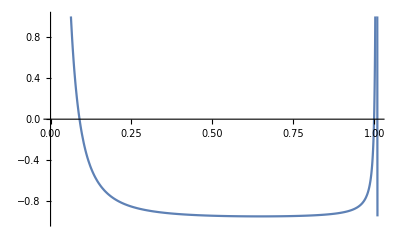
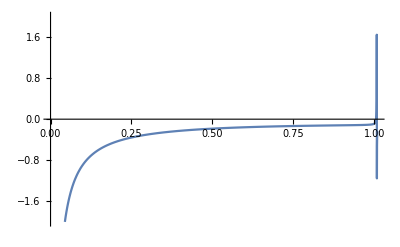
{{{0.123,0.001,0.0000999999},-Graphics-,-Graphics-},{{1.634,3.234,0.42},-Graphics-,-Graphics-},{{1.263,1.1,-7.62241×10^-12},-Graphics-,-Graphics-},{{1.643,1.01,-0.234},-Graphics-,-Graphics-},{{10.43,4.235,-10.234},-Graphics-,-Graphics-},{{46.6416,31.8489,-5.05572},-Graphics-,-Graphics-}}

```mathematica
Table[{CheckInputs[[i]],Plot[Function[{x,y,yt},Equation13[x,y,var,yt]]@@CheckInputs[[i]], {var,0, CheckInputs[[i, 2]]}, PlotRange->{Automatic, {-1, 1}}], Plot[Function[{x,y,yt},Equation14[x,y,var,yt]]@@CheckInputs[[i]], {var,0, CheckInputs[[i, 2]]}, PlotRange->{Automatic, {-2, 2}}]}, {i, 1, Length[CheckInputs]}]
```

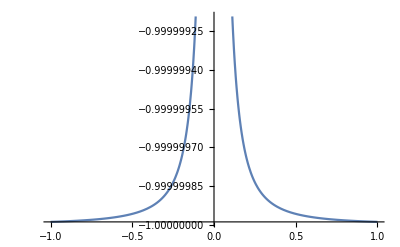
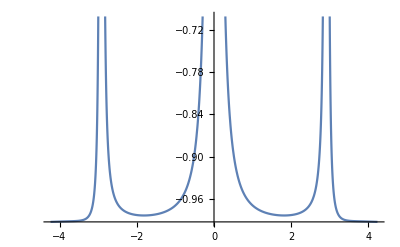
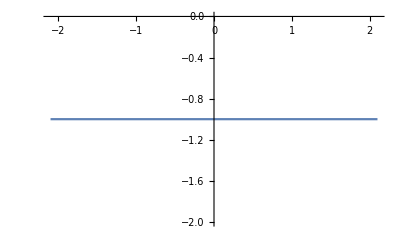
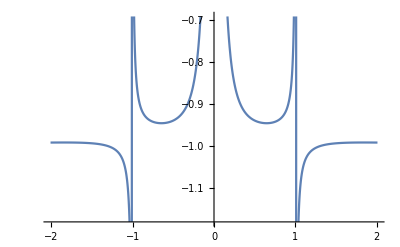
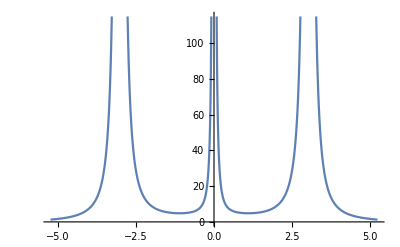
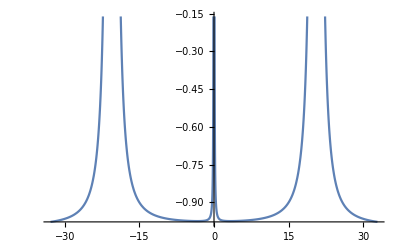

```mathematica
Table[Plot[Function[{x,y,yt},Equation13[x,y,var,yt]]@@CheckInputs[[i]], {var, -CheckInputs[[i, 2]] - 1, CheckInputs[[i, 2]] +1}], {i, 1, Length[CheckInputs]}]
```

```mathematica
FullSimplify[yt/(yp - 1/2 (y^2 - yp^2)1-2x (1-x)/(2 (1-x) - (y^2 - yp^2) + Sqrt[(y^2 - yp^2)^2 + 4(1-x)^2yp^2]))]
```

yt/(yp+1/2 (-y^2+yp^2)+(2 (-1+x) x)/(2-2 x-y^2+yp^2+√(4 (-1+x)^2 yp^2+(y^2-yp^2)^2)))

```mathematica
Plot[Function[{x,y,yt},Equation13[x,y,var,yt]]@@CheckInputs[[i]], {var,0, CheckInputs[[i, 2]]}, PlotRange->{Automatic, {-1, 1}}]//.i->1
 Plot[Function[{x,y,yt},Equation14[x,y,var,yt]]@@CheckInputs[[i]], {var,0, CheckInputs[[i, 2]]}, PlotRange->{Automatic, {-2, 2}}]//.i->1
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value {{0.123,0.001,0.0000999999},{1.634,3.234,0.42},{1.263,1.1,-7.62241×10^-12},{1.643,1.01,-0.234},{10.43,4.235,-10.234},{46.6416,31.8489,-5.05572}}⟦i,2⟧ in {var,0,{{0.123,0.001,0.0000999999},{1.634,3.234,0.42},{1.263,1.1,-7.62241×10^-12},{1.643,1.01,-0.234},{10.43,4.235,-10.234},{46.6416,31.8489,-5.05572}}⟦i,2⟧} is not a machine-sized real number.

-Graphics-

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value {{0.123,0.001,0.0000999999},{1.634,3.234,0.42},{1.263,1.1,-7.62241×10^-12},{1.643,1.01,-0.234},{10.43,4.235,-10.234},{46.6416,31.8489,-5.05572}}⟦i,2⟧ in {var,0,{{0.123,0.001,0.0000999999},{1.634,3.234,0.42},{1.263,1.1,-7.62241×10^-12},{1.643,1.01,-0.234},{10.43,4.235,-10.234},{46.6416,31.8489,-5.05572}}⟦i,2⟧} is not a machine-sized real number.

-Graphics-

```mathematica
Function[{x,y,yt},Equation14[x,y,0.00009999,yt]]@@CheckInputs[[1]]
Function[{x,y,yt},Equation13[x,y,0.0000999,yt]]@@CheckInputs[[1]]
```

0.999406

0.000610842